```mathematica
data=Table[{n,8.*(6*n!)/(1024^4)},{n,8,17}];
```

```mathematica
xl=Row[{Style["Number Particles ",FontFamily->"Latin Modern Roman",Plain,18],Style["N",FontFamily->"Latin Modern Roman",Italic,18],Style[" [1]",FontFamily->"Latin Modern Roman",Plain,18]}];
yl=DisplayForm[Row[{Style["Memory ",FontFamily->"Latin Modern Roman",Plain,18],Style["N!",FontFamily->"Latin Modern Roman",Italic,18],Style[" configurations [TB]",FontFamily->"Latin Modern Roman",Plain,18]}]];
```

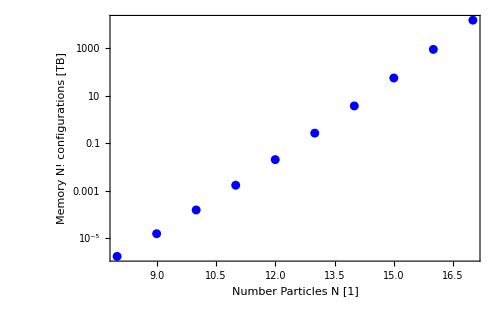

```mathematica
g=ListLogPlot[
data,
PlotStyle->Blue,
PlotRange->All,
ColorFunctionScaling->False,
PlotTheme->"Scientific",
FrameStyle->Directive[Black,FontColor->Black,15,FontFamily->"Latin Modern Roman",Plain],
FrameLabel->{xl,yl},
ImageSize->{500,500./GoldenRatio},
PlotRangePadding->0
]
```

```mathematica
Export["/home/tm/Projects/teatime_presentation/images/mem_1_config.png",g,ImageResolution->500];
```